```mathematica
<<"IGraphM`"
```

IGraph/M 0.6.5 (December 21, 2022)
Evaluate IGDocumentation[] to get started.

This part Generates a Graph with give μ and p.

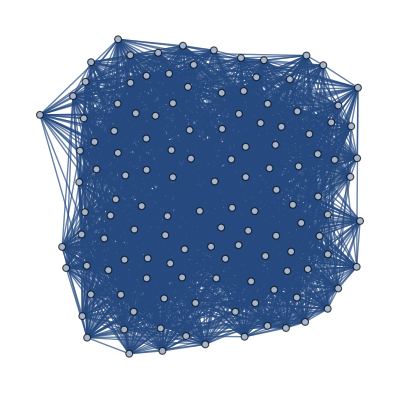

```mathematica
p=0.8;
μ=0.2;
u={0.1,0.2,0.3,0.4,0.5,0.6,0.7};
g=IGStochasticBlockModelGame[{{p,μ,μ,μ},{μ,p,μ,μ},{μ,μ,p,μ},{μ,μ,μ,p}},{32,32,32,32}]
```

This part Generates the same thing for μ = {0.1 , 0.2 , 0.3 , 0.4 , 0.5 , 0.6 , 0.7}

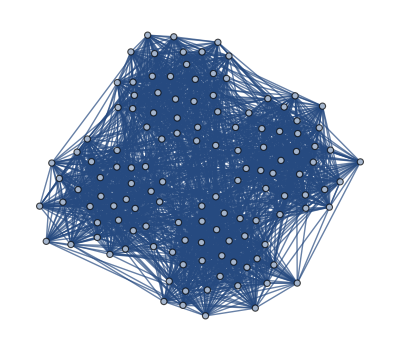
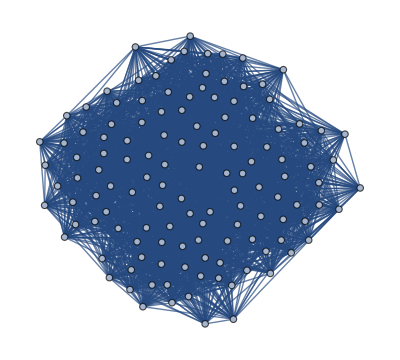
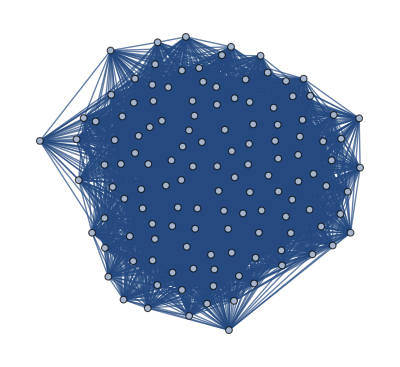
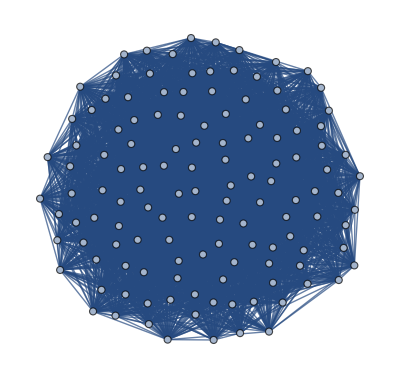
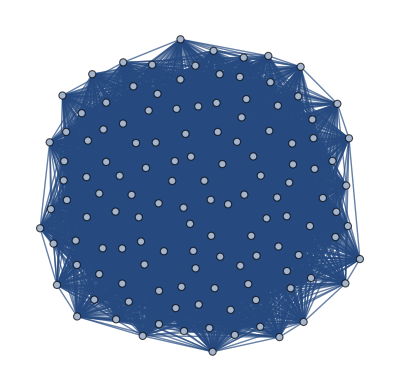
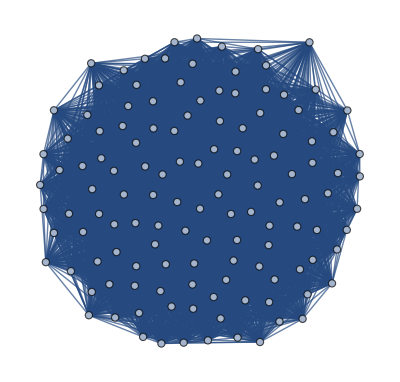
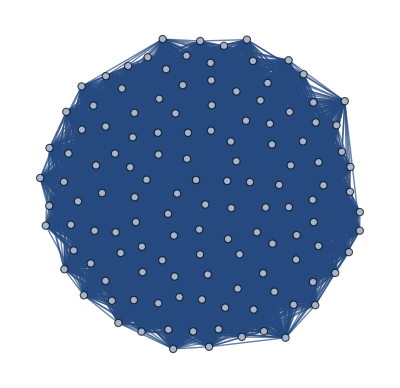

```mathematica
f=IGStochasticBlockModelGame[{{p,#,#,#},{#,p,#,#},{#,#,p,#},{#,#,#,p}},{32,32,32,32}]&/@u
```

This is the Adjacency Matrix of given graphs above

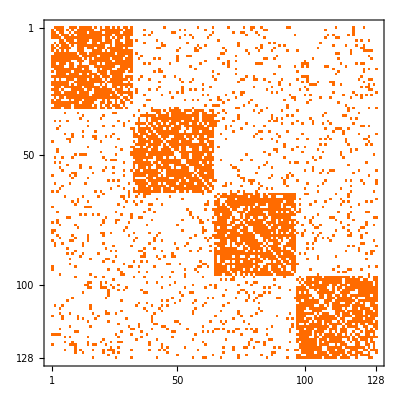
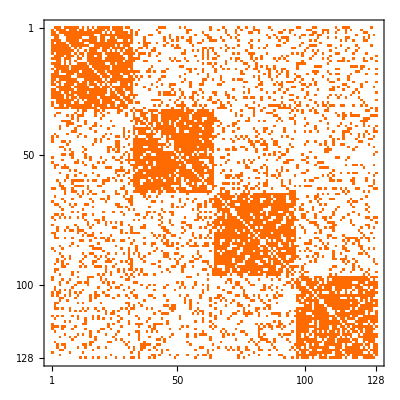
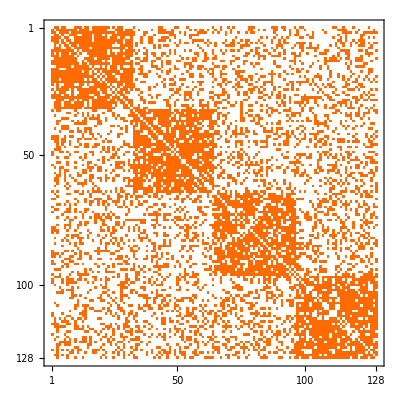
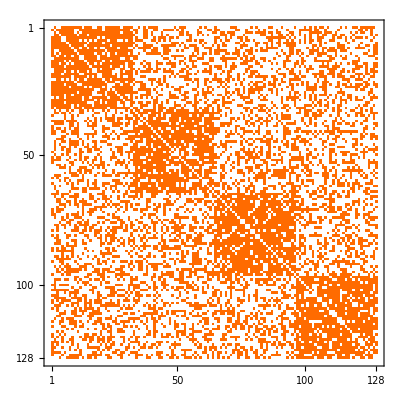
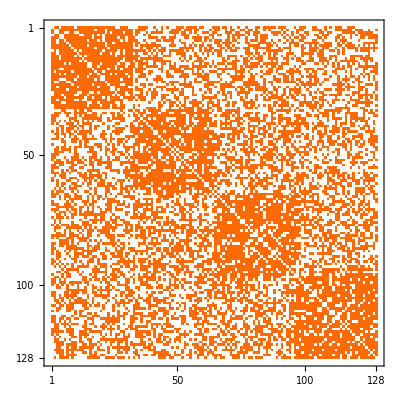
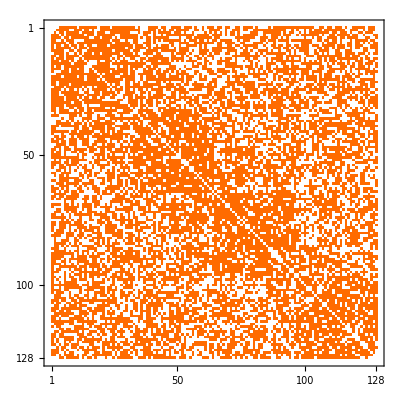
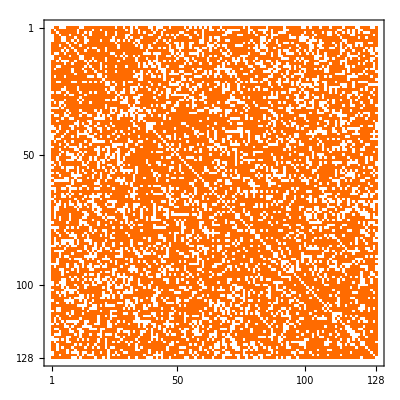

```mathematica
MatrixPlot[Normal[AdjacencyMatrix[#]]]&/@f
```

```mathematica
CommunityGraphPlot@#&/@f
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Com=FindGraphCommunities[#]&/@f
```

{{{33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,91},{70,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32},{65,66,67,68,69,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,92,93,94,95,96}},{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,60},{82,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128},{33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,61,62,63,64},{65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,83,84,85,86,87,88,89,90,91,92,93,94,95,96}},{{1,2,5,6,7,8,9,10,11,12,15,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,103,125},{3,4,13,14,16,17,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,120},{97,98,99,100,101,102,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,121,122,123,124,126,127,128}},{{1,2,4,5,8,9,10,11,12,14,15,16,17,19,20,22,23,24,25,26,27,28,29,31,97,99,100,101,102,104,105,106,107,108,109,112,113,114,115,118,120,121,122,123,124,125,126,127,128},{6,18,30,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,67,78,79,80,85,86,91,92,103,111,119},{3,7,13,21,65,66,68,69,70,71,72,73,74,75,76,77,81,82,83,84,87,88,89,90,93,94,95,96,98,110,116,117}},{{1,2,3,5,6,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,79,84,87,92,93,127},{4,7,27,65,66,67,68,69,70,71,72,73,74,75,76,77,78,80,81,82,83,85,86,88,89,90,91,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,128}},{{1,2,4,10,11,12,16,20,28,29,31,32,33,34,35,38,40,41,44,47,48,49,50,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,68,69,70,72,73,74,75,76,77,78,79,81,82,83,84,85,86,87,88,89,90,91,92,94,95,96,98,103,104,112,114,116,120,123},{3,5,6,7,8,9,13,14,15,17,18,19,21,22,23,24,25,26,27,30,36,37,39,42,43,45,46,51,67,71,80,93,97,99,100,101,102,105,106,107,108,109,110,111,113,115,117,118,119,121,122,124,125,126,127,128}},{{2,3,4,12,14,18,19,25,26,27,29,33,36,37,38,40,43,45,50,53,55,56,57,59,62,65,66,67,69,74,78,81,83,84,88,90,92,93,95,98,100,101,102,103,104,105,106,107,108,111,116,119,121,122,125,126,127,128},{1,6,7,8,9,10,11,13,16,20,21,22,23,24,28,30,32,35,39,41,42,44,48,49,51,54,58,60,63,64,68,70,71,72,73,75,77,79,80,82,86,87,89,94,96,99,109,110,112,113,114,115,118,120,123,124},{5,15,17,31,34,46,47,52,61,76,85,91,97,117}}}

This part calculates length of all communities with different methods for all the values of μ

```mathematica
Length/@Com[[#]]&/@{1,2,3,4,5,6,7}
```

{{33,33,32,30},{33,33,31,31},{60,39,29},{49,47,32},{67,61},{72,56},{58,56,14}}

```mathematica
Length/@(FindGraphCommunities[#]&/@f)[[#]]&/@{1,2,3,4,5,6,7}
```

{{33,33,32,30},{33,33,31,31},{60,39,29},{49,47,32},{67,61},{72,56},{58,56,14}}

```mathematica
Length/@(FindGraphCommunities[#,Method->"Modularity"]&/@f)[[#]]&/@{1,2,3,4,5,6,7}
```

{{33,33,32,30},{33,33,31,31},{60,39,29},{49,47,32},{67,61},{72,56},{58,56,14}}

```mathematica
Length/@(FindGraphCommunities[#,Method->"Hierarchical"]&/@f)[[#]]&/@{1,2,3,4,5,6,7}
```

{{32,32,32,32},{32,32,32,32},{33,32,32,31},{37,34,28,27,2},{38,35,22,7,4,4,3,3,3,2,2,1,1,1,1,1},{126,2},{128}}

```mathematica
Length/@(FindGraphCommunities[#,Method->"Spectral"]&/@f)[[#]]&/@{1,2,3,4,5,6,7}
```

{{33,32,31,29,3},{32,27,20,19,12,11,7},{32,32,32,32},{26,17,17,16,16,13,13,10},{20,18,16,14,10,8,8,7,7,7,6,4,3},{13,11,10,9,9,9,8,8,7,7,7,7,6,5,4,3,3,2},{15,12,11,10,10,9,8,8,8,7,6,5,5,4,4,3,2,1}}

```mathematica
Length/@(FindGraphCommunities[#,Method->"Centrality"]&/@f)[[#]]&/@{1,2,3,4,5,6,7}
```

$Aborted

```mathematica
Length/@(FindGraphCommunities[#,Method->"CliquePercolation"]&/@f)[[#]]&/@{1,2,3,4,5,6,7}
```

Now we want to know does the length of communities varies for different values of μ. The plot below is for hierarchical method.

```mathematica
h[x_]:=IGStochasticBlockModelGame[{{0.8,x,x,x},{x,0.8,x,x},{x,x,0.8,x},{x,x,x,0.8}},{32,32,32,32}]
```

```mathematica
data=Table[{x,Length/@FindGraphCommunities[h[x],Method->"Hierarchical"]},{x,0,1,0.01}];
```

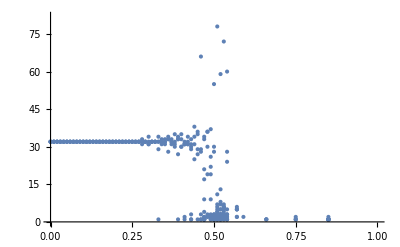

```mathematica
ListPlot[Flatten[Table[{data[[i,1]],data[[i,2,j]]},{i,1,Length[data]},{j,1,Length[data[[i,2]]]}],1]]
```

And this one is for the Modularity method.

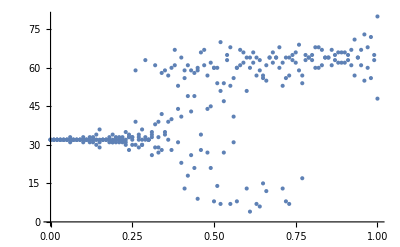

```mathematica
data2=Table[{x,Length/@FindGraphCommunities[h[x],Method->"Modularity"]},{x,0,1,0.01}];
ListPlot[Flatten[Table[{data2[[i,1]],data2[[i,2,j]]},{i,1,Length[data2]},{j,1,Length[data2[[i,2]]]}],1]]
```